```mathematica
f[x_,y_]=105 y^2+34 x y-110 y+3 x^2-18 x+29;
g[x_,y_]=(2-x-4 y)^2+(3-x-5 y)^2+(5-x-7 y)^2 ;
ContourPlot3D[{f[x,y,z]==0,g[x,y,z]==0},{x,-2,2},{y,-2,2},{z,-2,2},ContourStyle->Opacity[0.8],Mesh->None]
```

-Graphics3D-

```mathematica
pl1 = Plot3D[    {105/100 y^2+34/100 x y-110/100 y+3/100 x^2-18/100 x+29/100},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},105/100 y^2+34/100 x y-110/100 y+3/100 x^2-18/100 x+29/100 =  90/100 y^2+32/100 x y-116/100 y+3 /100x^2-20/100 x+38/100 ],BoxRatios->Automatic]
pl2 = Plot3D[    {90/100 y^2+32/100 x y-116/100 y+3 /100x^2-20/100 x+38/100},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic]
Show[pl1,pl2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-



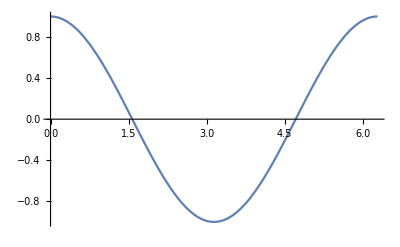

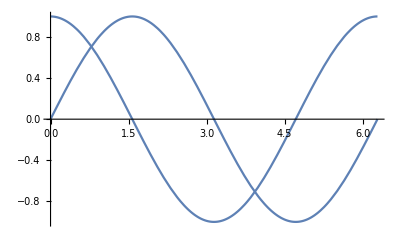

```mathematica
splot=Plot[Sin[x],{x,0,2 Pi}]
cplot=Plot[Cos[x],{x,0,2 Pi}]
Show[]
```

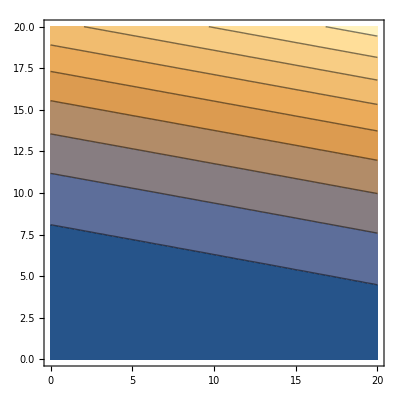

```mathematica
ContourPlot[105/100 y^2+34/100 x y-110/100 y+3/100 x^2-18/100 x+29/100 =  90/100 y^2+32/100 x y-116/100 y+3 /100x^2-20/100 x+38/100,{x,0,20},{y,0,20}]
```

```mathematica
Solve(105/100 y^2+34/100 x y-110/100 y+3/100 x^2-18/100 x+29/100 =  90/100 y^2+32/100 x y-116/100 y+3 /100x^2-20/100 x+38/100, {x,y})
```

```mathematica
Solve[105/100 y^2+34/100 x y-110/100 y+3/100 x^2-18/100 x+29/100 =  90/100 y^2+32/100 x y-116/100 y+3 /100x^2-20/100 x+38/100,{x,y},Reals]
```

Solve[19/50-x/5+(3 x^2)/100-(29 y)/25+(8 x y)/25+(9 y^2)/10,{x,y},ℝ]

```mathematica
Plot3D[{19/50-x/5+(3 x^2)/100-(29 y)/25+(8 x y)/25+(9 y^2)/10},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
splot=Plot3D[{(2-y-4x)^2 + (3-y-5x)^2},{x,-10,15}, {y,-10,20}, PlotStyle->Directive[Opacity[0.5],Green]]
cplot=Plot3D[{(2-y-4x)^2 + (7-y-1x)^2},{x,-10,15}, {y,-10,20}, PlotStyle->Directive[Opacity[0.5],Blue]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[splot,cplot]
```

-Graphics3D-

```mathematica
sol = Solve[(2-y-4x)^2 + (3-y-5x)^2 == (2-y-4x)^2 + (7-y-1x)^2, {x,y} ]
```

{{x→-1},{y→5-3 x}}

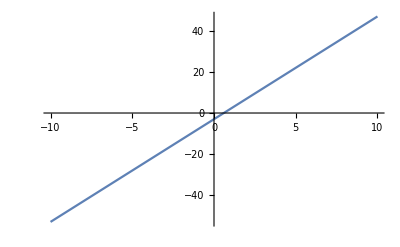

```mathematica
Plot[{5y-3}, {y,-10,10}]
```

```mathematica
Plot[k/.sol,{θ,0.5,10}]
```

```mathematica
Solve[{x,y}∈InfiniteLine[{{0,0},{2,1}}]&&{x,y}∈Circle[],{x,y}]
```

{{x→-2/(√5),y→-1/(√5)},{x→2/(√5),y→1/(√5)}}

```mathematica
ContourPlot3D[{(2-y-4x)^2 + (3-y-5x)^2 - z,(2-y-4x)^2 + (7-y-1x)^2 -z},{x,-100,20},{y,0,20},{z,0,20},Contours->{0},ContourStyle->Opacity[0],Mesh->None,BoundaryStyle->{1->None,2->None,{1,2}->{{Green,Tube[.09]}}},Boxed->True]
```

-Graphics3D-

```mathematica
ContourPlot3D[(2-y-4x)^2 + (3-y-5x)^2 - z==0,{x,-20,4},{y,0,20},{z,0,20},MeshFunctions->{Function[{x,y,z},(2-y-4x)^2 + (7-y-1x)^2 -z]},Mesh->{{0}},ContourStyle->None,PlotPoints->30,BoxRatios->Automatic]
```

-Graphics3D-

-Graphics3D-

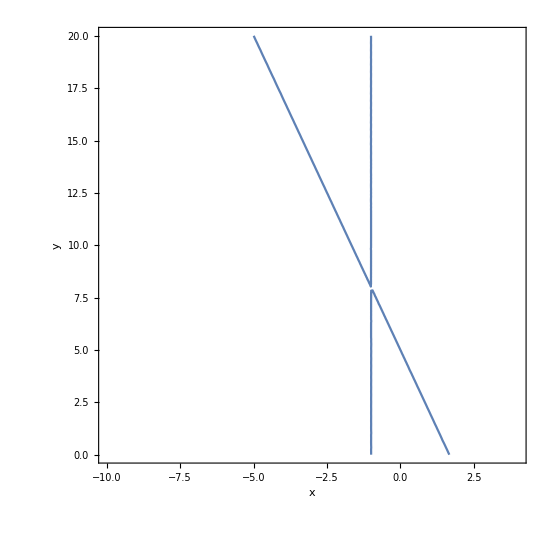

```mathematica
Show[splot,cplot]
ContourPlot[(2-y-4x)^2 + (3-y-5x)^2 == (2-y-4x)^2 + (7-y-1x)^2 ,{x,-10, 4},{y,0,20},PlotPoints->30,BoxRatios->Automatic, AxesLabel->Automatic]
```